```mathematica
(*Часть 1 (неправильная, можно листать дальше)*)
```

```mathematica
population=RecurrenceTable[{x[n+1]==r*x[n]*(1-x[n]),x[0]==x0},x,{n,1,5}];
```

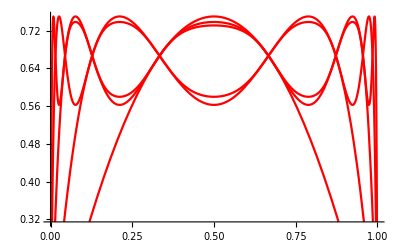

```mathematica
Plot[population/. r->3, {x0,0,1}, PlotStyle->Red]
```

```mathematica
(*В зависимости от времени при фиксированных r и x0 численность популяции возрастает, падает, затем снова возрастает и опять падает и тд. Чем дольше рассматриваемый отрезок времени, тем больше таких "волн" (их количество равно максимальной границе n)*)
```

```mathematica
Manipulate[Plot[population/. r->3,{x0, a-0.1, a+0.1}, PlotStyle->Purple],{a, 0, 1, 0.1}]
```

```mathematica
(*Вот так параметр х0 влияет на изменение численности (график вроде бы меняется более плавно)*)
```

```mathematica
Manipulate[Plot[population/. r->a,{x0,0,1}, PlotStyle->Blue],{a, 0, 5, 0.2}]
```

```mathematica
(*При увеличении r сначала график начинает расти быстрее, затем появляются волны - численность популяции становится нестабильной, после 4 значения покидают интервал [0,1] и уходят в отрицательные*)
```

```mathematica
(*Часть 1 переделанная*)
```

```mathematica
population[x0_,n_, r_]:=Module[{prev,curr, list},
list = {x0};
Do[prev = Last[list];
curr = r*prev*(1-prev);
AppendTo[list, curr], {i, 1, n}];Return[list]]
```

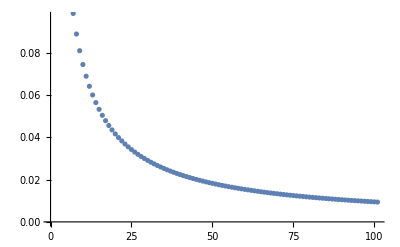

```mathematica
ListPlot[population[0.4, 100, 1]]
```

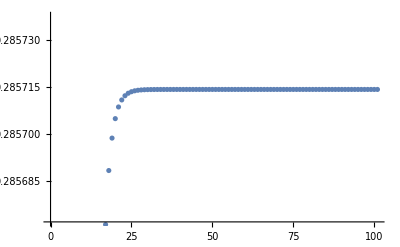

```mathematica
ListPlot[population[0.8, 100, 1.4]]
```

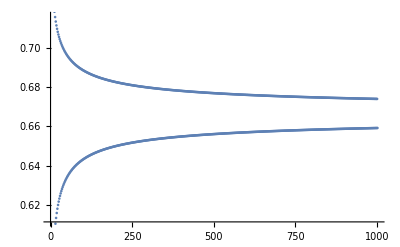

```mathematica
ListPlot[population[0.5, 1000, 3]]
```

```mathematica
(*при фиксированных x0 и r со временем последовательность начинает стремиться к определенному значению (или две ее ветки каждая к своему)*)
```

```mathematica
Manipulate[ListPlot[population[x0, 100, 1.4], PlotStyle->Purple],{x0, 0, 1, 0.1}]
```

ListPlot::lpn: population[1.,100.,1.4] is not a list of numbers or pairs of numbers.

```mathematica
Manipulate[ListPlot[population[x0, 100, 2], PlotStyle->Purple],{x0, 0, 1, 0.1}]
```

ListPlot::lpn: population[0.3,100.,2.] is not a list of numbers or pairs of numbers.

```mathematica
Manipulate[ListPlot[population[x0, 100, 3], PlotStyle->Purple],{x0, 0, 1, 0.1}]
```

ListPlot::lpn: population[1.,100.,3.] is not a list of numbers or pairs of numbers.

```mathematica
(*при изменении начального х0 требуется разное время для схождения последовательностей, они сходятся к разным значениям, а также между двумя ветками разное расстояние*)
```

```mathematica
Manipulate[ListPlot[population[0.9, 100, r], PlotStyle->Purple],{r, 0, 4, 0.2}]
```

ListPlot::lpn: population[0.9,100.,4.] is not a list of numbers or pairs of numbers.

```mathematica
Manipulate[ListPlot[population[0.5, 100, r], PlotStyle->Purple],{r, 0, 4, 0.2}]
```

ListPlot::lpn: population[0.5,100.,0.6] is not a list of numbers or pairs of numbers.

```mathematica
(*при изменении r и фиксированном x0 меняется характер динамики численности популяции: от 0 до 1 популяция довольно быстро сходится (сначала к 0, то есть вымирает, затем примерно от 1.5 к стабильному значению около начального), начиная от 2 ветки разделяются и приходят к хаосу при r=4 (при значениях больше 4 происходит overflow)*)
```

```mathematica
(*Часть 2*)
rList = {0};
```

```mathematica
Do[AppendTo[rList, Last[rList]+0.01],{i, 0,399}]
```

```mathematica
Length[rList]
```

401

```mathematica
pList={Partition[Riffle[{rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]]},population[0.5,100, rList[[1]]][[-10;;]]],2]}
```

{{{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.}}}

```mathematica
Do[pList=AppendTo[pList,Partition[Riffle[{rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]]},population[0.5,100, rList[[i]]][[-10;;]]],2]];,{i, 2, 401}]
```

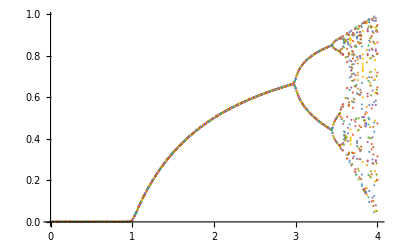

```mathematica
ListPlot[pList]
```

```mathematica
(*точность 0.01 по r*)
```

```mathematica
rList = {3};
```

```mathematica
Do[AppendTo[rList, Last[rList]+0.005],{i, 0,199}]
```

```mathematica
rList
```

{3,3.005,3.01,3.015,3.02,3.025,3.03,3.035,3.04,3.045,3.05,3.055,3.06,3.065,3.07,3.075,3.08,3.085,3.09,3.095,3.1,3.105,3.11,3.115,3.12,3.125,3.13,3.135,3.14,3.145,3.15,3.155,3.16,3.165,3.17,3.175,3.18,3.185,3.19,3.195,3.2,3.205,3.21,3.215,3.22,3.225,3.23,3.235,3.24,3.245,3.25,3.255,3.26,3.265,3.27,3.275,3.28,3.285,3.29,3.295,3.3,3.305,3.31,3.315,3.32,3.325,3.33,3.335,3.34,3.345,3.35,3.355,3.36,3.365,3.37,3.375,3.38,3.385,3.39,3.395,3.4,3.405,3.41,3.415,3.42,3.425,3.43,3.435,3.44,3.445,3.45,3.455,3.46,3.465,3.47,3.475,3.48,3.485,3.49,3.495,3.5,3.505,3.51,3.515,3.52,3.525,3.53,3.535,3.54,3.545,3.55,3.555,3.56,3.565,3.57,3.575,3.58,3.585,3.59,3.595,3.6,3.605,3.61,3.615,3.62,3.625,3.63,3.635,3.64,3.645,3.65,3.655,3.66,3.665,3.67,3.675,3.68,3.685,3.69,3.695,3.7,3.705,3.71,3.715,3.72,3.725,3.73,3.735,3.74,3.745,3.75,3.755,3.76,3.765,3.77,3.775,3.78,3.785,3.79,3.795,3.8,3.805,3.81,3.815,3.82,3.825,3.83,3.835,3.84,3.845,3.85,3.855,3.86,3.865,3.87,3.875,3.88,3.885,3.89,3.895,3.9,3.905,3.91,3.915,3.92,3.925,3.93,3.935,3.94,3.945,3.95,3.955,3.96,3.965,3.97,3.975,3.98,3.985,3.99,3.995,4.}

```mathematica
pList={Partition[Riffle[{rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]]},population[0.5,100, rList[[1]]][[-10;;]]],2]};
```

```mathematica
Do[pList=AppendTo[pList,Partition[Riffle[{rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]]},population[0.5,100, rList[[i]]][[-10;;]]],2]];,{i, 2, Length[rList]}]
```

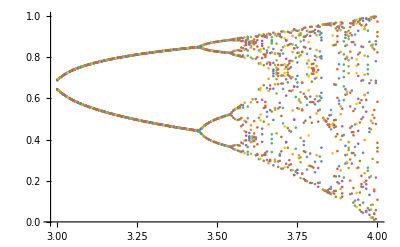

```mathematica
ListPlot[pList]
```

```mathematica
(*точность 0,005 - шаг по r*)
```

```mathematica
(*после r=3 происходят бифуркации: решения раздваиваются и так далее, около 4 и дальше предсказать численность популяции на следующем шаге становится невозможным.*)
```

```mathematica
(*Часть 3*)
```

```mathematica
(*при r > 4 происходит overflow. что это значит с точки зрения математики? вероятно, происходит огромный разброс значений, либо их очень много, так как период разделения - это степени двойки, и разделения становятся ближе => видимо после 4 чисел уже огромное количество. не надо вычислять эту функцию при r > 4. просто не надо.*)
```

```mathematica
(*Часть 4*)
```

```mathematica
rList = {2.8};
```

```mathematica
Do[AppendTo[rList, Last[rList]+0.0025],{i, 0,479}]
```

```mathematica
rList;
```

```mathematica
pList={Partition[Riffle[{rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]],rList[[1]]},population[0.5,100, rList[[1]]][[-10;;]]],2]};
```

```mathematica
Do[pList=AppendTo[pList,Partition[Riffle[{rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]],rList[[i]]},population[0.5,100, rList[[i]]][[-10;;]]],2]];,{i, 2, Length[rList]}]
```

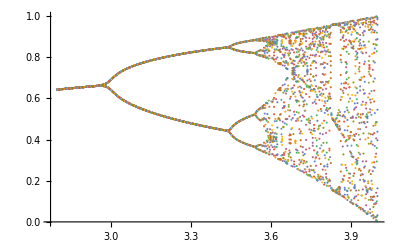

```mathematica
pltF = ListPlot[pList]
```

```mathematica
lst1 = population[0.5,100, 2.8][[-10;;]]
```

{0.642857,0.642857,0.642857,0.642857,0.642857,0.642857,0.642857,0.642857,0.642857,0.642857}

```mathematica
lst2 = population[0.5,100, 3.2][[-10;;]]
```

{0.799455,0.513045,0.799455,0.513045,0.799455,0.513045,0.799455,0.513045,0.799455,0.513045}

```mathematica
lst3 = population[0.5,100, 3.5][[-10;;]]
```

{0.826941,0.500884,0.874997,0.38282,0.826941,0.500884,0.874997,0.38282,0.826941,0.500884}

```mathematica
(*можно заметить, что у бифуркаций существует период: до раздвоения все значения похожи, после - каждое третье, затем - каждое пятое и тд. возможно, критическую точку можно распознать по изменению периода*)
```

```mathematica
(*вот функция, которая показывает, какие значения уже имеют 2 ветки. возьмем то из них, которое упоминается первым и добавим в список r, которые мы будем отображать, а затем сделаем похожие функции для 2, 4 и т.д. веток. Интрвал для приближения поиска будем выбирать по графику*)
```

```mathematica
checkP2[r_,lstr_]:=(
lst = population[0.5,100, r][[-10;;]];
Do[d0=0;
d = 0;
d = Abs[lst[[i]]-lst[[i+1]]];
If[d>d0, d0=d;];,
{i, 1, 9}];
(*Print[r];*)
(*Print[d0];*)
If[d0>0.0001,Print["Remember " , r];Break;];
)
```

```mathematica
Do[checkP2[i, lstr], {i, 2.8, 3, 0.0025}]
```

Remember 2.9325

Remember 2.935

Remember 2.9375

Remember 2.94

Remember 2.9425

Remember 2.945

Remember 2.9475

Remember 2.95

Remember 2.9525

Remember 2.955

Remember 2.9575

Remember 2.96

Remember 2.9625

Remember 2.965

Remember 2.9675

Remember 2.97

Remember 2.9725

Remember 2.975

Remember 2.9775

Remember 2.98

Remember 2.9825

Remember 2.985

Remember 2.9875

Remember 2.99

Remember 2.9925

Remember 2.995

Remember 2.9975

Remember 3.

```mathematica
lstr = {2.9324999999999997}
```

{2.9325}

```mathematica
Clear[lst, i, d, d0]
```

```mathematica
(*проверка расчетверения веток*)
```

```mathematica
checkP4[r_,lstr_]:=(
lst = population[0.5,100, r][[-10;;]];
Do[d0=0;
d = 0;
d = Abs[lst[[i]]-lst[[i+2]]];
If[d>d0, d0=d;];,
{i, 1, 8}];
(*Print[r];*)
(*Print[d0];*)
If[d0>0.0001,Print["Remember " , r];Break;];
)
```

```mathematica
Do[checkP4[i, lstr], {i, 3.3, 3.5, 0.0025}]
```

Remember 3.4275

Remember 3.43

Remember 3.4325

Remember 3.435

Remember 3.4375

Remember 3.44

Remember 3.4425

Remember 3.445

Remember 3.4475

Remember 3.45

Remember 3.4525

Remember 3.455

Remember 3.4575

Remember 3.46

Remember 3.4625

Remember 3.465

Remember 3.4675

Remember 3.47

Remember 3.4725

Remember 3.475

Remember 3.4775

Remember 3.48

Remember 3.4825

Remember 3.485

Remember 3.4875

Remember 3.49

Remember 3.4925

Remember 3.495

Remember 3.4975

Remember 3.5

```mathematica
AppendTo[lstr,3.4274999999999998]
```

{2.9325,3.4275}

```mathematica
Clear[lst, i, d, d0]
```

```mathematica
checkP8[r_,lstr_]:=(
lst = population[0.5,100, r][[-10;;]];
Do[d0=0;
d = 0;
d = Abs[lst[[i]]-lst[[i+4]]];
If[d>d0, d0=d;];,
{i, 1, 6}];
(*Print[r];*)
(*Print[d0];*)
If[d0>0.0001,Print["Remember " , r];Break;];
)
```

```mathematica
Do[checkP8[i, lstr], {i, 3.5, 3.55, 0.0025}]
```

Remember 3.5375

Remember 3.54

Remember 3.5425

Remember 3.545

Remember 3.5475

Remember 3.55

```mathematica
AppendTo[lstr, 3.5375]
```

{2.9325,3.4275,3.5375}

```mathematica
Clear[lst, i, d, d0]
```

```mathematica
checkP16[r_,lstr_]:=(
lst = population[0.5,100, r][[-10;;]];
Do[d0=0;
d = 0;
d = Abs[lst[[i]]-lst[[i+8]]];
If[d>d0, d0=d;];,
{i, 1, 2}];
(*Print[r];*)
(*Print[d0];*)
If[d0>0.0001,Print["Remember " , r];Break;];
)
```

```mathematica
Do[checkP16[i, lstr], {i, 3.53, 3.6, 0.0025}]
```

Remember 3.54

Remember 3.5425

Remember 3.545

Remember 3.5625

Remember 3.565

Remember 3.5675

Remember 3.57

Remember 3.5725

Remember 3.575

Remember 3.5775

Remember 3.58

Remember 3.5825

Remember 3.585

Remember 3.5875

Remember 3.59

Remember 3.5925

Remember 3.595

Remember 3.5975

Remember 3.6

```mathematica
AppendTo[lstr, 3.5399999999999996]
```

{2.9325,3.4275,3.5375,3.54}

```mathematica
(*далее проверять не имеет смысла, так как 16 веток не видны на графике при такой точности, к тому же при запоминаемых последних 10 значениях функции период 16 уже нельзя проверить*)
```

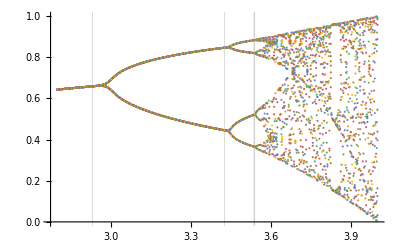

```mathematica
ListPlot[pList, GridLines->{{lstr[[1]], lstr[[2]], lstr[[3]], lstr[[4]]},{}}]
```

```mathematica
(*можно заметить, что 3 и 4 линии слиплись - значит там происходит хаос
рассмотрим первую линию внимательнее*)
```

```mathematica
rList1 = {2.8};
```

```mathematica
Do[AppendTo[rList1, Last[rList1]+0.0025],{i, 0,100}]
```

```mathematica
pList1={Partition[Riffle[{rList1[[1]],rList1[[1]],rList1[[1]],rList1[[1]],rList1[[1]],rList1[[1]],rList1[[1]],rList1[[1]],rList1[[1]],rList1[[1]]},population[0.5,100, rList1[[1]]][[-10;;]]],2]};
```

```mathematica
pList1
```

{{{2.8,0.642857},{2.8,0.642857},{2.8,0.642857},{2.8,0.642857},{2.8,0.642857},{2.8,0.642857},{2.8,0.642857},{2.8,0.642857},{2.8,0.642857},{2.8,0.642857}}}

```mathematica
Do[pList1=AppendTo[pList1,Partition[Riffle[{rList1[[i]],rList1[[i]],rList1[[i]],rList1[[i]],rList1[[i]],rList1[[i]],rList1[[i]],rList1[[i]],rList1[[i]],rList1[[i]]},population[0.5,100, rList1[[i]]][[-10;;]]],2]];,{i, 2, Length[rList1]}]
```

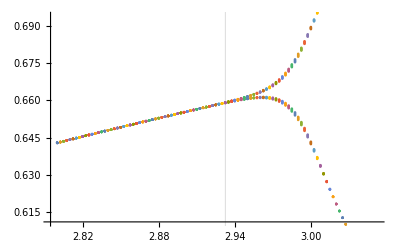

```mathematica
ListPlot[pList1, GridLines->{{lstr[[1]]},{}}]
```

```mathematica
(*вероятно здесь решения отличаются уже достаточно, чтобы быть раздвоением по значениям, но не выглядеть так.
можно пересчитать для меньшей точности:*)
```

```mathematica
checkP2[r_,lstr_]:=(
lst = population[0.5,100, r][[-10;;]];
Do[d0=0;
d = 0;
d = Abs[lst[[i]]-lst[[i+1]]];
If[d>d0, d0=d;];,
{i, 1, 9}];
(*Print[r];*)
(*Print[d0];*)
If[d0>0.001,Print["Remember " , r];Break;];
)
```

```mathematica
Do[checkP2[i, lstr], {i, 2.8, 3, 0.0025}]
```

Remember 2.955

Remember 2.9575

Remember 2.96

Remember 2.9625

Remember 2.965

Remember 2.9675

Remember 2.97

Remember 2.9725

Remember 2.975

Remember 2.9775

Remember 2.98

Remember 2.9825

Remember 2.985

Remember 2.9875

Remember 2.99

Remember 2.9925

Remember 2.995

Remember 2.9975

Remember 3.

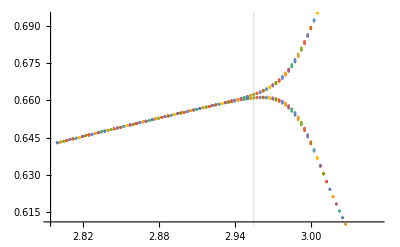

```mathematica
ListPlot[pList1, GridLines->{{2.9549999999999996},{}}]
```

```mathematica
(*это выглядит более похожим на раздвоение, но в данном случае сложно понять, какой критерий раздвоения: на сколько должны отличаться значения, чтобы они считались разными ветками*)
```

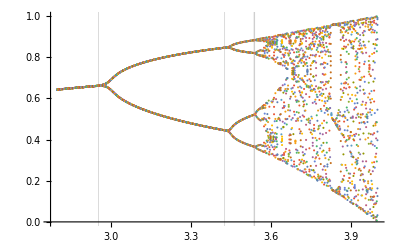

```mathematica
ListPlot[pList, GridLines->{{2.9549999999999996, lstr[[2]], lstr[[3]], lstr[[4]]},{}}]
```